# Hybrid Computation : Prime Factorization

#### Abhishek Sharma Cronin Lab University of Glasgow

## Direct Method Prime Factorization : Hamiltonian Formulation

Consider a l-bit integer N=p×q where p and q are the prime numbers. This factorization problem can be described as an optimization problem by defining the function f(x,y)=(N-x y)^2 where variables x and y are positive integers. Using [1], the number of bits required for n_x and n_y are given by,

n_x= m(⌊√N⌋_o) -1<= ⌊(l+1)/2⌋-1
n_y= m(⌊N/3⌋) -1<= l-1

[1] Quantum Adiabatic Algorithm for Factorization and Its Experimental Implementation, Phys. Rev. Lett. 101, 220405
[2] Quantum Annealing for Prime Factorization,  Sci Rep 8, 17667 (2018)

```mathematica
num=21; (* Number for the Prime Factorization *)
```

```mathematica
nX[num_]:= With[{fsqnum=Floor[√num]},Length@IntegerDigits[If[OddQ[fsqnum],fsqnum,fsqnum-1],2]-1];
nY[num_]:= With[{fsqnum=Floor[num/3]},Length@IntegerDigits[fsqnum,2]-1];
totalStates[num_]:=nX[num]+nY[num];
```

```mathematica
nQ[num_]:=Table[Symbol["x"<>ToString[i]],{i,totalStates[num]}];(* Defining spins as symbols for Ising Model Formulation *)
```

```mathematica
varsX=nQ[num][[1;;nX[num]]]; (* Spin variables for first number *)
varsY=nQ[num][[nX[num]+1;;totalStates[num]]]; (* Spin variables for second number *)
varsAll=Flatten@{varsX,varsY}
```

{x1,x2,x3}

```mathematica
pN=1+Total@Table[varsX[[i]] 2^i,{i,Length@varsX}]
```

1+2 x1

```mathematica
qN=1+Total@Table[varsY[[i]] 2^i,{i,Length@varsY}]
```

1+2 x2+4 x3

```mathematica
Ham=Expand[FullSimplify[(num-pN qN)^2]]
```

400-80 x1+4 x1^2-80 x2-152 x1 x2+16 x1^2 x2+4 x2^2+16 x1 x2^2+16 x1^2 x2^2-160 x3-304 x1 x3+32 x1^2 x3+16 x2 x3+64 x1 x2 x3+64 x1^2 x2 x3+16 x3^2+64 x1 x3^2+64 x1^2 x3^2

```mathematica
HamN=Ham/.((#^2->#)&/@varsAll)
```

400-76 x1-76 x2-104 x1 x2-144 x3-144 x1 x3+16 x2 x3+128 x1 x2 x3

```mathematica
rule=x1 x2 x3-> x4 x3 + 2(x1 x2 -2 x1 x4 -2 x2 x4 +3x4)
```

x1 x2 x3→x3 x4+2 (x1 x2+3 x4-2 x1 x4-2 x2 x4)

```mathematica
QuboToIsingRule=Block[{n,s},Table[Symbol["x"<>ToString[i]]->1/2 (1-Symbol[("s"<>ToString[i])]),{i,Length@nQ[num]+1}]] (* Rule for converting Ising to QUBO *)
```

{x1→(1-s1)/2,x2→(1-s2)/2,x3→(1-s3)/2,x4→(1-s4)/2}

```mathematica
HamF=Expand[FullSimplify[HamN/.rule]/.QuboToIsingRule]
```

418+164 s1+124 s2+38 s1 s2+72 s3-36 s1 s3+4 s2 s3-160 s4-128 s1 s4-128 s2 s4+32 s3 s4

```mathematica
nS={s1,s2,s3,s4}
```

{s1,s2,s3,s4}

```mathematica
quadTerms=Union[#⟦1⟧ #⟦2⟧&/@Tuples[nS,{2}]] (* Collecting Quadratic Terms *)
```

{s1^2,s1 s2,s2^2,s1 s3,s2 s3,s3^2,s1 s4,s2 s4,s3 s4,s4^2}

```mathematica
c2=Coefficient[HamF,quadTerms] (* Getting coefficients of all the quadratic terms *)
```

{0,38,0,-36,4,0,-128,-128,32,0}

```mathematica
linearTerms=HamF-Coefficient[HamF,quadTerms].quadTerms (* Getting coefficients of all linear terms *)
```

418+164 s1+124 s2+72 s3-160 s4

```mathematica
p=Coefficient[linearTerms,nS].Evaluate[#^2&/@nS] (* Changing linear terms to quadratic terms *)
```

164 s1^2+124 s2^2+72 s3^2-160 s4^2

```mathematica
q=c2.quadTerms (* Initial Quadratic Terms *)
```

38 s1 s2-36 s1 s3+4 s2 s3-128 s1 s4-128 s2 s4+32 s3 s4

```mathematica
offSet=First@Cases[Ham,_Integer] (* Offset term *)
```

400

```mathematica
HamQUBO=Expand[p+q+offSet](* Adding all terms and getting the full Hamiltonian for QUBO formulation *)
```

400+164 s1^2+38 s1 s2+124 s2^2-36 s1 s3+4 s2 s3+72 s3^2-128 s1 s4-128 s2 s4+32 s3 s4-160 s4^2

```mathematica
HamQUBO0 = offSet
```

400

```mathematica
HamQUBO1=Coefficient[HamQUBO,Evaluate[#^2&/@nS]]
```

{164,124,72,-160}

```mathematica
rules=Flatten@MapThread[{#1->#2}&,{quadTerms,Coefficient[HamQUBO,quadTerms]}]
```

{s1^2→164,s1 s2→38,s2^2→124,s1 s3→-36,s2 s3→4,s3^2→72,s1 s4→-128,s2 s4→-128,s3 s4→32,s4^2→-160}

```mathematica
selfInteraction=Block[{mat=Evaluate[#^2&/@nS]},MapThread[{#1,#2}&,{mat, Evaluate[mat/.rules]}]]
```

{{s1^2,164},{s2^2,124},{s3^2,72},{s4^2,-160}}

```mathematica
pairInteraction=Block[{mat=Union[#⟦1⟧ #⟦2⟧&/@Permutations[nS,{2}]],matCoeff},
matCoeff=ToExpression[StringSplit[ToString[#],"s"]]&/@mat;
MapThread[{#1,#2}&,{matCoeff, Evaluate[mat/.rules]}]]
```

{{{1,2},38},{{1,3},-36},{{2,3},4},{{1,4},-128},{{2,4},-128},{{3,4},32}}

Creating a two dimensional matrix to describe the fully coupled neighbour-neighbour interaction

```mathematica
twoPairArray=ConstantArray[0,{Length[nS],Length[nS]}];
```

```mathematica
(twoPairArray⟦#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧⟧=1/2#⟦2⟧)&/@pairInteraction;
```

```mathematica
twoPairArrayF=twoPairArray+ Transpose[twoPairArray];twoPairArrayF//MatrixForm
```

(0 | 19 | -18 | -64
19 | 0 | 2 | -64
-18 | 2 | 0 | 16
-64 | -64 | 16 | 0)

```mathematica
HamQUBO2=twoPairArrayF;HamQUBO2//MatrixForm (* Factorizing out the greatest common divisor *)
```

(0 | 19 | -18 | -64
19 | 0 | 2 | -64
-18 | 2 | 0 | 16
-64 | -64 | 16 | 0)

```mathematica
totalMat =DiagonalMatrix[HamQUBO1]+ twoPairArrayF;totalMat//MatrixForm
```

(164 | 19 | -18 | -64
19 | 124 | 2 | -64
-18 | 2 | 72 | 16
-64 | -64 | 16 | -160)

```mathematica
(1/(PolynomialGCD@@Flatten[totalMat])totalMat)//MatrixForm
```

(164 | 19 | -18 | -64
19 | 124 | 2 | -64
-18 | 2 | 72 | 16
-64 | -64 | 16 | -160)

## Solving using Stochastic Gradient Descent Method

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
calculateEnergy[state_,Ham0_,Ham1_,Ham2_]:= Module[{pairwise,singleTerms,coupledTerms},singleTerms=Total[state Ham1];
pairwise=Subsets[Range@Length[state],{2}];
coupledTerms=2.Total[(Ham2⟦#⟦1⟧,#⟦2⟧⟧&/@pairwise)(state⟦#⟦1⟧⟧state⟦#⟦2⟧⟧&/@pairwise)];
Ham0+singleTerms+coupledTerms]
```

```mathematica
calculateGradients[state_,Ham1_,Ham2_]:=Module[{singleTerms,coupledTerms,grad,m1,m2,ff,p1,p2},singleTerms=Ham1;
m1=DeleteCases[Range[Length@state],#]&/@Range[Length@state];
m2=ConstantArray[#,Length[state]-1]&/@Range[Length@state];
ff=MapThread[Transpose[{#1,#2}]&,{m1,m2}];
p1=Table[Ham2⟦#⟦1⟧,#⟦2⟧⟧&/@ff⟦i⟧,{i,Length@ff}];
p2=Table[state⟦#⟧&/@m1⟦i⟧,{i,Length@ff}];
coupledTerms=Table[p1⟦i⟧.p2⟦i⟧,{i,Length@p1}];
grad = singleTerms + 2 coupledTerms]
```

```mathematica
updateStates[state_,fac_,Ham1_,Ham2_,noiseMax_]:=Module[{grad,gradCorrected,gradNorm,norm,rem=0},grad=calculateGradients[state,Ham1, Ham2];gradCorrected=Piecewise[{{0.,state⟦#⟧<-1+10^-8 && grad⟦#⟧>0},{0.,state⟦#⟧>1-10^-8 && grad⟦#⟧<0}},rem++;grad⟦#⟧]&/@Range[Length@grad];
gradNorm=If[Total[Abs[gradCorrected]]> 1 10^-10&&rem>0,norm=Total[Abs[gradCorrected]]/rem;gradCorrected/norm,grad];
Piecewise[{{1,#>1},{-1.,#<-1}},#]&/@(state- RandomReal[{-noiseMax/2,noiseMax/2},Length@nS]-fac (gradNorm))]
```

```mathematica
initStates = RandomReal[{-1,1},Length@nS]
```

{0.811224,-0.495715,0.547757,-0.99879}

```mathematica
stateF={};
```

```mathematica
run[steps_]:=Monitor[Block[{state=initStates,energy},energy=Table[state=updateStates[state,0.2,HamQUBO1,HamQUBO2,1.];
calculateEnergy[state,HamQUBO0,HamQUBO1,HamQUBO2],{i,steps}];PrintTemporary["Final State : ", state, " Energy :", Last@energy];
stateF=Join[stateF,{state}];energy],i];
```

```mathematica
dataPlot=Table[Clear[initStates];initStates = RandomReal[{-1,1},Length@nS];run[200],{i,50}];
```

```mathematica
Dimensions@dataPlot
```

{50,200}

```mathematica
Dimensions@stateF
```

{50,4}

```mathematica
plot1=ListPlot[(Last[dataPlot⟦#1⟧]&)/@Range[Length[dataPlot]],FrameLabel->{"Run No.","Energy"},Frame->True,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{Black,PointSize[0.015]},Filling->Axis,ImageSize->300];
```

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.01],Length@dataPlot],ConstantArray[Opacity[0.5],Length@dataPlot],ColorData[56,#]&/@Range[Length@dataPlot]}];
```

```mathematica
plot2=ListPlot[dataPlot,PlotRange->All,PlotStyle->plotStyle,Frame->True,FrameLabel->{"Time Step", "Energy"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300];
```

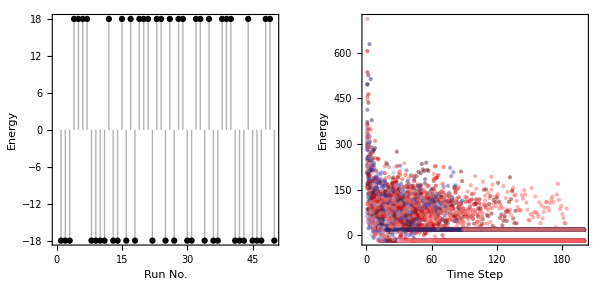

```mathematica
GraphicsRow[{plot1,plot2},ImageSize->600]
```

```mathematica
solnPos=With[{finalE=Last@#&/@dataPlot},Flatten@Position[finalE,Min@finalE]]
```

{1,2,3,8,9,10,11,13,14,16,18,22,25,27,30,31,34,36,37,41,42,43,45,46,47,50}

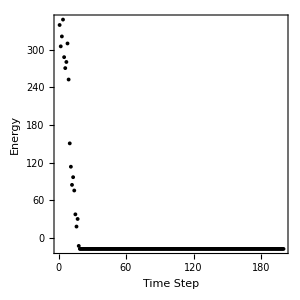

```mathematica
ListPlot[dataPlot[[solnPos[[3]]]],PlotRange->All,Frame->True,FrameLabel->{"Time Step", "Energy"},AspectRatio->1,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

```mathematica
solnsS=With[{finalE=Last@#&/@dataPlot},stateF[[#]]&/@Flatten@Position[finalE,Min@finalE]];
```

```mathematica
{x1,x2,x3,x4}=IntegerPart@((1-#)/2)&/@solnsS[[1]]
```

{1,1,1,1}

Hence, the solution is given by :

```mathematica
{num,{pN,qN}}
```

{21,{3,7}}